## Teoría de Tomografía de muones

## Dispersión Múltiple de Coulomb, Muones

#### Usando dispersión múltiple de Coulomb para segregar materiales de Alto, Medio y Bajo número atómico Z

Al salir del material, la nueva trayectoria del muón puede describirse mediante los ángulos de dispersión proyectados θx, θy y los desplazamientos ∆x, ∆y donde todos estos [REF: Schultz, Thesis, Cosmic Ray Radiography].

Una aproximación gaussiana simple funciona bien para el 98 % central de la distribución de dispersión. Para uno de los ángulos de dispersión proyectados, θx :

f_θ_x(θ_x)≅1/(√(2π)σ_θ)exp(-θ_x^2/(2 σ_θ^2))

De misma forma el ángulo proyectado  θy, es independiente pero idénticamentedistribuido a θx.

f_θ_y(θ_y)≅1/(√(2π)σ_θ)exp(-θ_y^2/(2 σ_θ^2))

De forma que para los dos planos es:

f_θ(θ)≅1/(√(2π)σ_θ)exp(-θ^2/(2 σ_θ^2))

Que es definida para una media(μ = 0) y varianza σ_θ^2. Según,  [REF: Bae,Momentum-Dependent Cosmic Ray Muon Computed Tomography Using a Fieldable Muon Spectrometer].

f(θ| 0,σ_θ^2)=1/(√(2π)σ_θ)exp(-1/2 *θ^2/σ_θ^2)   ;
 σ_θ = (13.6 MeV)/(β_μ p_μ c)√(L/L_o)[1+0.088Log(L/L_o)]

θ -> ángulo de dispersión, σ_θ-> es el ancho de la Distro. de Gauss de dispersión, 
L -> grosor del medio de dispersión, Lo-> longitud de radiación, β_μ-> el la taza del velocidad de la luz del muon(c), p_μ->momento del muon.

Según, [REF : Bonomi, Apps . cosmic - ray muons, Review ...] y [REF : Particle Data Group], el RMS(σ) es. La raíz cuadrada media (rms) de la aproximación gaussiana de la distribución angular proyectada se ha calculado y se puede expresar de la siguiente manera .

σ_θ=(13.6MeV)/βcp*z*√(X/Xo)*(1+0.038*ln((x z^2)/(Xo β^2)))
X -> grosor del medio de dispersión, Xo-> longitud de radiación, βc->  velocidad del muon(~1),z->carga de la psrtícula (muon es 1), p->momento del muon.

#### Gráfica de Gauss de ángulo de dispersión, Para un medio de 10 cm de Pb [REF : Bae, Momentum - Dependent ...]

Ecuacion según [ REF : Bae, Momentum - Dependent Cosmic Ray Muon Computed Tomography Using a Fieldable Muon Spectrometer]

```mathematica
(*Constantes*)βc= 1(*factor beta de luz*);L=10(*grosor cm*);Lo=6.37 (*Lrad, Pb g/cm^2*);p=3*10^9(*momento 3GeV, TODO en eV*);StdSigma=(13.6*10^6)/(βc*p)*√(L/Lo)*(1+0.088*Log[L/Lo]);
f[θ_]:=1/(√(2*π)*StdSigma)*Exp[-1/2*θ^2/StdSigma^2];
```

¡ OJO ! el término de la exponencial se hace muy chiquito  ya que la expresión de la varianza es muy grande y contribuye de maner sustancial a la forma aprox. de  ⅇ^(-α θ^2), para un α muy grande, lo cual genera valores muy pequeños.

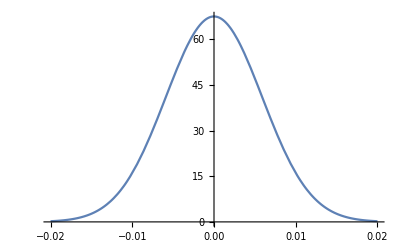

```mathematica
Plot[f[θ],{θ,-2*10^-2,2*10^-2}]
```

Entonces deben de existir ángulos en el orden de 10^-2a 10^-3rads. Para que no explote la Gauss.

#### Gráfica de Gauss de ángulo de dispersión, Para un medio de 10 cm de Pb [REF : Bonomi, Apps. cosmic-ray muons, Review ...] y [REF : PDG, Review of Particle Physics, cosmic-ray muons ...]

Ejemplo.

```mathematica
(*Constantes*)βc= 1(*factor beta de luz*);β=1;X=10(*grosor cm*);Xo=6.37 (*Lrad, Pb g/cm^2*);p=3*10^9(*momento 3GeV*);z=1(*carga*);StdSigma2=(13.6*10^6)/(βc*p)*z*√(X/Xo)*(1+0.038*Log[ⅇ,(X*z^2)/(Xo*β^2)]);ff[θ_]:=1/(√(2*π)*StdSigma2)*Exp[-θ^2/(2*StdSigma2^2)];
```

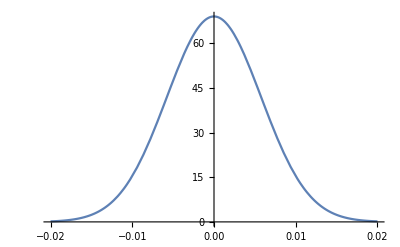

```mathematica
Plot[ff[θ],{θ,-2*10^-2,2*10^-2}]
```

#### OTRO Para 10 cm de Pb

```mathematica
DataTheta=RandomVariate[NormalDistribution[0,StdSigma2],3*10^3];
```

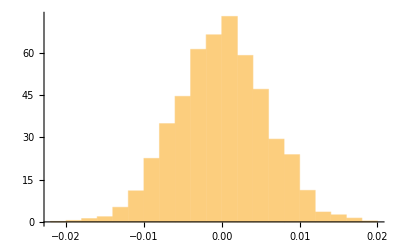

```mathematica
Histogram[DataTheta,20,"ProbabilityDensity"]
```

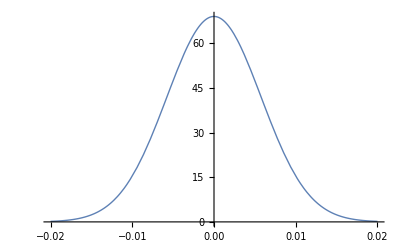

```mathematica
Plot[PDF[NormalDistribution[0,StdSigma2],x],{x,-2*10^-2,2*10^-2},PlotStyle->Thick]
```

#### 10 cm Pb, y 10 cm Si, momento de 3GeV

```mathematica
StdSigmaPb=(13.6*10^6)/(βc*p)*√(10/Xo)*(1+0.038*Log[ⅇ,(10*z^2)/(Xo*β^2)]);(*Pb*)
StdSigmaSi=(13.6*10^6)/(βc*p)*√(10/21.82)*(1+0.038*Log[ⅇ,(10*z^2)/(21.82*β^2)]);(*Si*)
```

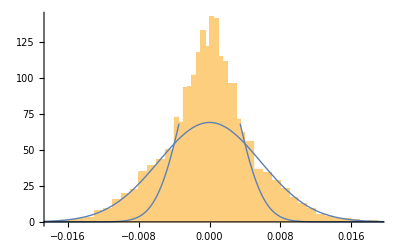

```mathematica
DataPb=RandomVariate[NormalDistribution[0,StdSigmaPb],3*10^3];
DataSi=RandomVariate[NormalDistribution[0,StdSigmaSi],3*10^3];
HistPb=Histogram[DataPb,30,"ProbabilityDensity"];
HistSi=Histogram[DataSi,30,"ProbabilityDensity"];
PDFPb=Plot[PDF[NormalDistribution[0,StdSigmaPb],x],{x,-2*10^-2,2*10^-2},PlotStyle->Thick];
PDFSi=Plot[PDF[NormalDistribution[0,StdSigmaSi],x],{x,-3*10^-2,3*10^-2},PlotStyle->Thick];
Show[{HistPb,HistSi,PDFPb,PDFSi}]
```

#### Cálculo de la varianza y gráfica FALLIDO

Cálculo de la varianza de dispersión en función del grosor del material de dispersión, de plomo.

```mathematica
(*Constantes*)β = 1;cLight = 1;(*Longt. rads de Pb->tablas [g/cm^2]]*)L0=6.37 ;
```

```mathematica
VarSigma[Thickness_,pMomentum_]:=(0.0136/(β*pMomentum*cLight)√(Thickness/L0)(1+0.088*Log[10,Thickness/L0]))^2;
```

```mathematica
DesvSigma[Thickness_,pMomentum_]:=0.0136/(β*pMomentum*cLight)√(Thickness/L0)(1+0.088*Log[10,Thickness/L0]);
```

```mathematica
{DesvSigma[0.1,3],VarSigma[0.1,3]*10^3}
```

{0.000360357,0.000129857}

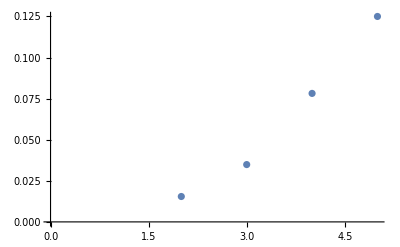

```mathematica
ListPlot[Table[VarSigma[L,3]*10^3,{L,{0,5,10,20,30}}]]
```

Con las funciones de arriba no es posible reproducir la gráfica de la varianza del ángulo de dispersión de [REF : Bae, Momentum - Dependent Cosmic Ray Muon Computed Tomography Using a Fieldable Muon Spectrometer].

Al parecer hay que seguir una construcción de varianza descrito en [REF : Bae, The Effect of Cosmic Ray Muon Momentum Measurement for Monitoring Shielded Special
   Nuclear Materials].

## Tomo Caso 2

REF : [Simulations and Track Reconstruction for Muon Tomography 
   using Resistive Plate Chambers, R . Sehgal]

El ancho de la distribución del ángulo desviado, es decir la desviació típica según la teoría de MCS (multiple coulmb scatering) es de la forma de:

σ_θ=(13.6(*MeV*))/(β c p)√(X/X_0)[1+0.038*Ln(X/X_0)])

Desviación típica

```mathematica
sigmaTheta[L_,Lo_]:=(1.36*10^7(*eV*))/(β*c*p)*√(L/Lo)*(1+0.038*Log[L/Lo]);
```

```mathematica
(*Constantes*)
β= 0.9(*factor beta de luz*);p=(2*10^9)/c(* 3 GeV, TODO en eV*);
(*L [cm] y Lo [g/cm^2]*)
```

Caso 1 Aluminio

```mathematica
(*Lo = 24.01 [g/cm^2] *)
```

```mathematica
xPts1={2.5,4,4.5,8,10,12,15,18};
yPts1=N[Table[sigmaTheta[i,24.01],{i,xPts1}]*1000(*mrad*),4];
```

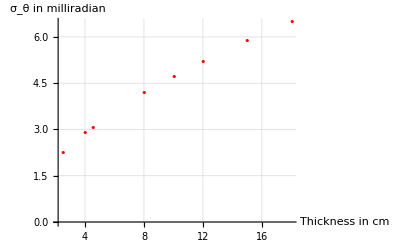

```mathematica
P1=ListPlot[Transpose[{xPts1,yPts1}],PlotRange->All,PlotStyle->Red,AxesLabel->{"Thickness in cm " ,"σ_θ in milliradian"},GridLines->Automatic,PlotMarkers->"•"]
```

Caso 2 Fierro

```mathematica
(*Lo = 13.84 [g/cm^2] *)
```

```mathematica
xPts2={2.5,4,4.5,8,10,12,15,18};
yPts2=N[Table[sigmaTheta[i,13.84],{i,xPts2}]*1000(*mrad*),4];
```

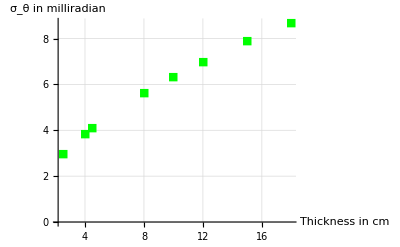

```mathematica
P2=ListPlot[Transpose[{xPts2,yPts2}],PlotRange->All,PlotStyle->Green,AxesLabel->{"Thickness in cm " ,"σ_θ in milliradian"},GridLines->Automatic,PlotMarkers->"■"]
```

Caso 3 Plomo

```mathematica
(*Lo = 6.37[g/cm^2] *)
```

```mathematica
xPts3={2.5,4,4.5,8,10,12,15,18};
yPts3=N[Table[sigmaTheta[i,6.37],{i,xPts3}]*1000(*mrad*),4];
```

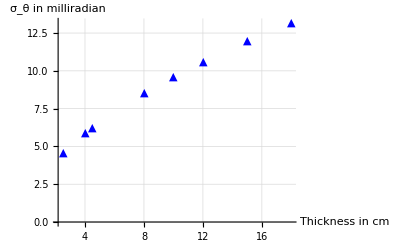

```mathematica
P3= ListPlot[Transpose[{xPts3,yPts3}],PlotRange->All,PlotStyle->Blue,AxesLabel->{"Thickness in cm " ,"σ_θ in milliradian"},GridLines->Automatic,PlotMarkers->"▲"]
```

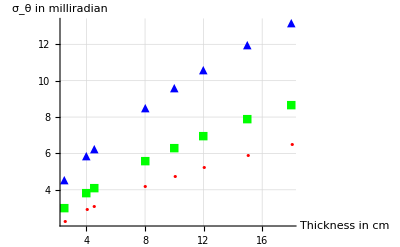

```mathematica
Show[{P1,P2,P3},PlotRange->All]
```

Las gráficas muestran como claramente se observa que a medida que el elemento (z mayor) es más denso la desviación típica del ángulo de disperión es mayor, por lo que se pueden indentificar claramente los materiales. σ_θ> para Z mayores.